```mathematica
Timing[
$HistoryLength=3;
ClearAll[Lz,XY,XZ,YZ];
Lz=20;(*Lengrh of simulation*)
R=0.08;(*Solenoid radius*)
q=1.60217657*10^-19;(*Elementary charge*)

(*List of initial particle velosity and energy*)

Rad[1]={"-3e4","-2.4e4","-1.8e4","-1.2e4","-6e3","0","6e3","1.2e4","1.8e4","2.4e4","3e4"};
Eneg[1]={"4.823e5","1.928e6","1.198e7","4.705e7","1.763e8","3.633e8","5.870e8","8.333e8","1.094e9","1.365e9","1.641e9","1.923e9","2.208e9"};

Table[orb[i,j]=Import["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/solenoid_scipy/result/pthe_finit_ne/pthe_finit_sl4cm/alldata_amp4e-2_velo"<>ToString[Rad[1][[j]]]<>"_kene"<>ToString[Eneg[1][[i]]]<>"_sleng4cm_step8001.dat","Table"],{i,1,13},{j,1,11}];

LENG[1]=Length[orb[1,1]];
Table[X[i,j]=orb[i,j][[All,1]],{i,1,13},{j,1,11}];
Table[Vx[i,j]=orb[i,j][[All,2]],{i,1,13},{j,1,11}];
Table[Y[i,j]=orb[i,j][[All,3]],{i,1,13},{j,1,11}];
Table[Vy[i,j]=orb[i,j][[All,4]],{i,1,13},{j,1,11}];
Table[Z[i,j]=orb[i,j][[All,5]],{i,1,13},{j,1,11}];
Table[Vz[i,j]=orb[i,j][[All,6]],{i,1,13},{j,1,11}];
Table[Xy[i,j]=orb[i,j][[All,{1,3}]],{i,1,13},{j,1,11}];
Table[RZ[i,j]=Table[{Z[i,j][[n]],(X[i,j][[n]]^2+Y[i,j][[n]]^2)^0.5},{n,1,LENG[1]}],{i,1,13},{j,1,11}];
Table[PT[i,j]=orb[i,j][[All,{5,7}]],{i,1,13},{j,1,11}];
Table[RK[i,j]=orb[i,j][[All,8]],{i,1,13},{j,1,11}];

(*List of rigidity and beta*gamma*)

Brho[1]={0.1,0.2,0.5,1,2,3,4,5,6,7,8,9,10};
betag[1]={0.03218,0.06439,0.16092,0.3218,0.64368,0.9655,1.2874,1.6092,1.931,2.2529,2.5747,2.8966,3.2184};

Table[ToRK[i,j]={Abs[PT[i,j][[1,2]]]*10^6/(Brho[1][[i]]*q/betag[1][[i]]),Abs[Sum[RK[i,j][[n]]*Vz[i,j][[n]]*(Lz/((Vz[i,j][[1]])*(LENG[1]-1))),{n,1,LENG[1]}]]},{i,1,13},{j,1,11}];

]
```

{223.91171,Null}

```mathematica
(*Calculation of theoretical radial kick*)

l=0.04;(*Length of Solenoid*)
Bz00[z_]=(z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2));(*Bz field*)
Bz1[z_]:=((z+l/2)/(√((z+l/2)^2+R^2))-(z-l/2)/(√((z-l/2)^2+R^2)))/Bz00[0];(*Scaled Bz field*)
Bz2[z_]:=Bz1'[z];(*1st differential of Bz field*)
Bz3[z_]:=Bz2'[z];(*2nd differential of Bz field*)
Bz4[z_]:=Bz3'[z];(*3rd differential of Bz field*)
Bz5[z_]:=Bz4'[z];(*4th differential of Bz field*)
Bz6[z_]:=Bz5'[z];(*5th differential of Bz field*)
Bz7[z_]:=Bz6'[z];(*6th differential of Bz field*)

Timing[
Table[RD1[i,j]=-1/4*NIntegrate[(Bz1[z]/(Brho[1][[i]]))^2*√(X[i,j][[3853]]^2+Y[i,j][[3853]]^2),{z,-∞,∞}],{i,1,13},{j,1,11}];
Table[RD2[i,j]=-1/8*NIntegrate[(Bz2[z]/(Brho[1][[i]]))^2*√(X[i,j][[3853]]^2+Y[i,j][[3853]]^2)^3,{z,-∞,∞}],{i,1,13},{j,1,11}];
Table[RD3[i,j]=-5/256*NIntegrate[(Bz3[z]/(Brho[1][[i]]))^2*√(X[i,j][[3853]]^2+Y[i,j][[3853]]^2)^5,{z,-∞,∞}],{i,1,13},{j,1,11}];
Table[RD4[i,j]=-7/4608*NIntegrate[(Bz4[z]/(Brho[1][[i]]))^2*√(X[i,j][[3853]]^2+Y[i,j][[3853]]^2)^7,{z,-∞,∞}],{i,1,13},{j,1,11}];
Table[RD5[i,j]=-7/98304*NIntegrate[(Bz5[z]/(Brho[1][[i]]))^2*√(X[i,j][[3853]]^2+Y[i,j][[3853]]^2)^9,{z,-∞,∞}],{i,1,13},{j,1,11}];
Table[RD6[i,j]=-11/4915200*NIntegrate[(Bz6[z]/(Brho[1][[i]]))^2*√(X[i,j][[3853]]^2+Y[i,j][[3853]]^2)^11,{z,-∞,∞}],{i,1,13},{j,1,11}];
Table[RD7[i,j]=-143/2831155200*NIntegrate[(Bz7[z]/(Brho[1][[i]]))^2*√(X[i,j][[3853]]^2+Y[i,j][[3853]]^2)^13,{z,-∞,∞}],{i,1,13},{j,1,11}];

Table[TheoToRKP1[i,j]={PT[i,j][[1,2]]*10^6/(Brho[1][[i]]*q/betag[1][[i]]),-RD1[i,j]},{i,1,13},{j,1,11}];

Table[TheoToRKP[i,j]={PT[i,j][[1,2]]*10^6/(Brho[1][[i]]*q/betag[1][[i]]),-(RD1[i,j]+RD2[i,j]+RD3[i,j]+RD4[i,j]+RD5[i,j]+RD6[i,j]+RD7[i,j])},{i,1,13},{j,1,11}];
]
```

{21.71632,Null}

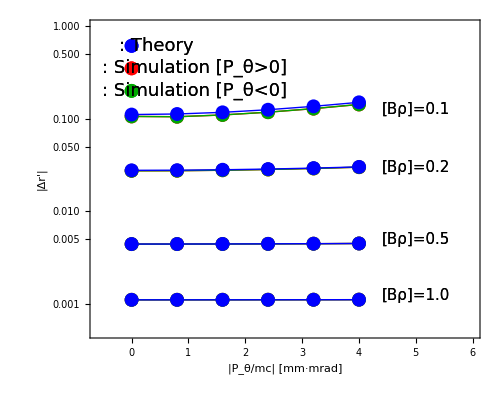

```mathematica
(*LogPlot of comparison between theory and simulations*)

GList[1]={{{5,2.5/2*10^-1}},{{5,0.6/2*10^-1}},{{5,1/2*10^-2}},{{5,2.5/2*10^-3}}};

GList[2]={{{0.43,1.225/2}},{{1.1,0.7/2}},{{1.1,0.4/2}}};

Comp[1]=Show[
ListLogPlot[Table[ToRK[1,i],{i,6,11,1}],PlotRange->{{-0.6,6},{0.0005,1}},FrameLabel->{"|P_θ/mc| [mm·mrad]","|Δr'|"},LabelStyle->Directive[18],Frame->True,AspectRatio->0.8,Axes->None,Joined->True,PlotStyle->{Red},ImageSize->{500,400}],
ListLogPlot[Table[ToRK[1,i],{i,6,11,1}],PlotRange->{{0,1},{0.000001,0.1}},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListLogPlot[Table[ToRK[1,i],{i,6,1,-1}],PlotRange->{{-0.0000006,0.000006},{0.001,2}},FrameLabel->{"P_θ/mc [m·rad]","|Δr'|"},LabelStyle->Directive[18],Frame->True,AspectRatio->0.8,Axes->None,Joined->True,PlotStyle->{Darker[Green]},ImageSize->{500,400}],
ListLogPlot[Table[ToRK[1,i],{i,6,1,-1}],PlotRange->{{0,1},{0.000001,0.1}},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Darker[Green],PointSize[0.02]}],
ListLogPlot[Table[TheoToRKP[1,i],{i,6,11,1}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Blue}],
ListLogPlot[Table[TheoToRKP[1,i],{i,6,11,1}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]}],

ListLogPlot[Table[ToRK[2,i],{i,6,11,1}],PlotRange->{{-0.0000006,0.000006},{0.001,2}},FrameLabel->{"|P_θ/mc| [m·rad]","|Δr'|"},LabelStyle->Directive[18],Frame->True,AspectRatio->0.8,Axes->None,Joined->True,PlotStyle->{Red},ImageSize->{500,400}],
ListLogPlot[Table[ToRK[2,i],{i,6,11,1}],PlotRange->{{0,1},{0.000001,0.1}},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListLogPlot[Table[ToRK[2,i],{i,6,1,-1}],PlotRange->{{-0.0000006,0.000006},{0.001,2}},FrameLabel->{"P_θ/mc [m·rad]","|Δr'|"},LabelStyle->Directive[18],Frame->True,AspectRatio->0.8,Axes->None,Joined->True,PlotStyle->{Darker[Green]},ImageSize->{500,400}],
ListLogPlot[Table[ToRK[2,i],{i,6,1,-1}],PlotRange->{{0,1},{0.000001,0.1}},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Darker[Green],PointSize[0.02]}],
ListLogPlot[Table[TheoToRKP[2,i],{i,6,11,1}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Blue}],
ListLogPlot[Table[TheoToRKP[2,i],{i,6,11,1}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]}],

ListLogPlot[Table[ToRK[3,i],{i,6,11,1}],PlotRange->{{-0.0000006,0.000006},{0.001,2}},FrameLabel->{"|P_θ/mc| [m·rad]","|Δr'|"},LabelStyle->Directive[18],Frame->True,AspectRatio->0.8,Axes->None,Joined->True,PlotStyle->{Red},ImageSize->{500,400}],
ListLogPlot[Table[ToRK[3,i],{i,6,11,1}],PlotRange->{{0,1},{0.000001,0.1}},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListLogPlot[Table[ToRK[3,i],{i,6,1,-1}],PlotRange->{{-0.0000006,0.000006},{0.001,2}},FrameLabel->{"P_θ/mc [m·rad]","|Δr'|"},LabelStyle->Directive[18],Frame->True,AspectRatio->0.8,Axes->None,Joined->True,PlotStyle->{Darker[Green]},ImageSize->{500,400}],
ListLogPlot[Table[ToRK[3,i],{i,6,1,-1}],PlotRange->{{0,1},{0.000001,0.1}},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Darker[Green],PointSize[0.02]}],
ListLogPlot[Table[TheoToRKP[3,i],{i,6,11,1}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Blue}],
ListLogPlot[Table[TheoToRKP[3,i],{i,6,11,1}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]}],

ListLogPlot[Table[ToRK[4,i],{i,6,11,1}],PlotRange->{{-0.0000006,0.000006},{0.001,2}},FrameLabel->{"|P_θ/mc| [m·rad]","|Δr'|"},LabelStyle->Directive[18],Frame->True,AspectRatio->0.8,Axes->None,Joined->True,PlotStyle->{Red},ImageSize->{500,400}],
ListLogPlot[Table[ToRK[4,i],{i,6,11,1}],PlotRange->{{0,1},{0.000001,0.1}},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Red,PointSize[0.02]}],
ListLogPlot[Table[ToRK[4,i],{i,6,1,-1}],PlotRange->{{-0.0000006,0.000006},{0.001,2}},FrameLabel->{"P_θ/mc [m·rad]","|Δr'|"},LabelStyle->Directive[18],Frame->True,AspectRatio->0.8,Axes->None,Joined->True,PlotStyle->{Darker[Green]},ImageSize->{500,400}],
ListLogPlot[Table[ToRK[4,i],{i,6,1,-1}],PlotRange->{{0,1},{0.000001,0.1}},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Darker[Green],PointSize[0.02]}],
ListLogPlot[Table[TheoToRKP[4,i],{i,6,11,1}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,Joined->True,PlotStyle->{Blue}],
ListLogPlot[Table[TheoToRKP[4,i],{i,6,11,1}],PlotRange->{{0,1},All},FrameLabel->{"r/R","r''"},LabelStyle->Directive[15],Frame->True,Axes->None,PlotStyle->{Blue,PointSize[0.02]}],

ListLogPlot[GList[1],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{"[Bρ]=0.1",15},{"[Bρ]=0.2",15},{"[Bρ]=0.5",15},{"[Bρ]=1.0",15}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListLogPlot[GList[2],PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Black},PlotMarkers->{{": Theory",18},{": Simulation [P_θ>0]",18},{": Simulation [P_θ<0]",18}},BaseStyle->{FontFamily->"Times",FontSize->15}],

ListLogPlot[{{-0.25*10^-6,1.225/2}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Blue,PointSize[0.02]}],
ListLogPlot[{{-0.25*10^-6,0.7/2}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Red,PointSize[0.02]}],
ListLogPlot[{{-0.25*10^-6,0.4/2}},PlotRange->All,LabelStyle->Directive[15],PlotStyle->{Darker[Green],PointSize[0.02]}]
]
```

```mathematica
(*Export graphic data to the directory on your computer:you have to specify the directory where you want to export*)

Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Pthetaf/Pthef_Comp_Sum_sol4cm.eps",Comp[1],"EPS"];
```